```mathematica
Arlist1={0.0,2.3,4.0,6.1,8.0,10.0,11.0,11.5,12.2,12.7,13.1,13.5,14.0,14.5,15.0,15.5,16.0,16.5,17.0,17.3,17.6,18.0,18.3,18.6,19.1,19.4,19.8,20.1,20.6,21.0,21.4,22.1,22.5,23.0,23.5,23.9,24.3,24.6,25.1,25.4,25.8,26.0,26.4,26.8,27.0,27.4,27.8,28.2,28.5,28.9,29.2,29.7,30.0,30.5,31.0,31.6,32.2,32.6,33.1,33.3,33.7,34.2,34.5,35.0,35.4,35.8,36.2,36.6,37.0,37.4,37.8,38.7,39.0,39.3,39.8,40.0,40.3,40.6,41.0,41.5,42.0,43.0,43.5,44.1,44.5,45.0,45.5,46.0,46.5,47.0,47.5,48.2,48.6,49.0,49.5,50.1,51.0,52.1,52.5,53.0,53.5,54.5,56.0,57.3,58.0,59.0,60.0,61.0,62.0,62.5,63.0,63.4,63.7,64.1,64.4,64.7,65.1,65.5,66.0,67.1,68.0,69.0,70.1,71.1,72.0,73.0,74.0,75.0,76.0,76.5,76.8,77.2,77.6,78.0,78.5,79.2,80.0,81.0,82.0,82.5,83.0,83.6,84.0,84.5,85.0};
Arlist2={19.6,20.0,19.8,19.5,19.0,20.1,30.0,39.0,72.2,112.2,123.6,135.0,148.0,155.6,163.1,163.5,169.6,171.0,174.6,172.6,171.7,171.5,173.5,170.2,154.3,148.4,133.4,122.6,97.2,77.4,56.5,44.1,57.1,97.1,155.2,188.8,235.5,240.2,280.4,292.2,318.5,318.2,338.4,350.1,351.6,364.0,374.2,376.3,368.8,361.2,349.0,320.9,293.1,236.4,179.1,101.3,43.0,18.4,16.9,29.2,60.3,118.6,153.5,220.4,257.0,301.4,325.3,365.9,394.9,416.1,430.2,461,471,475,481,473,469,461,437,404,332,178,103,40,31,47,92,149,207,253,319,382,417,448,486,517,553,567,552,533,486,354,165,108,158,282,387,473,555,578,602,617,628,637,638,636,626,611,583,475,367,276,265,315,385,480,574,649,710,730,738,745,746,741,725,691,634,557,497,489,487,496,510,532,564};
```

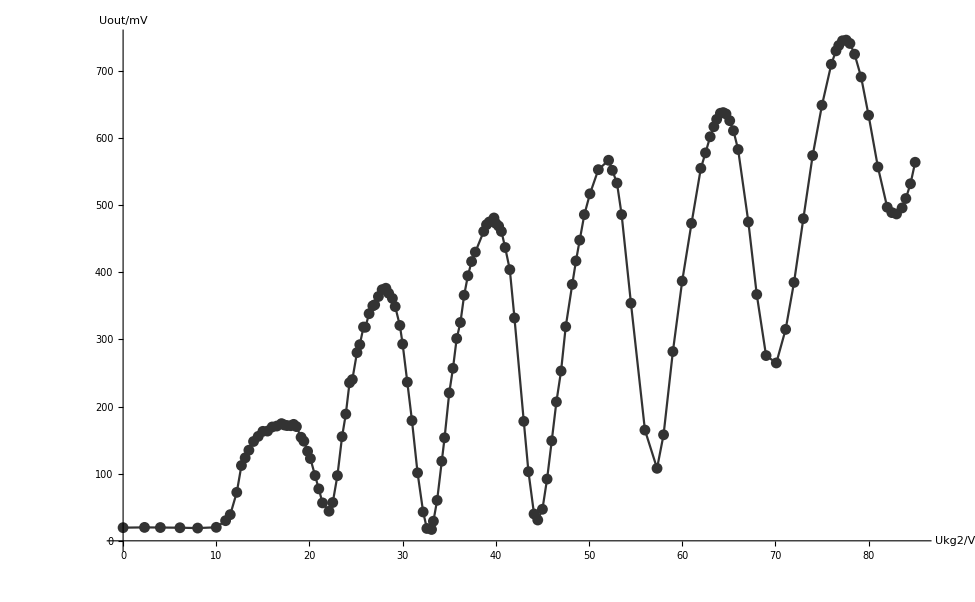

```mathematica
Show[ListPlot[Table[{Arlist1[[i]],Arlist2[[i]]},{i,1,Length[Arlist1]}],PlotStyle->{PointSize[0.008],Lighter[Black,0.2]}],ListLinePlot[Table[{Arlist1[[i]],Arlist2[[i]]},{i,1,Length[Arlist1]}],PlotStyle->{PointSize[0.008],Lighter[Black,0.2]}],AxesLabel->{"Ukg2/V","Uout/mV"}]
```

```mathematica
Arlist1[[88]]
```

46.

```mathematica
Grid[{Arlist1[[1;;40]],Arlist2[[1;;40]]},Frame->All]
```

0. | 2.3 | 4. | 6.1 | 8. | 10. | 11. | 11.5 | 12.2 | 12.7 | 13.1 | 13.5 | 14. | 14.5 | 15. | 15.5 | 16. | 16.5 | 17. | 17.3 | 17.6 | 18. | 18.3 | 18.6 | 19.1 | 19.4 | 19.8 | 20.1 | 20.6 | 21. | 21.4 | 22.1 | 22.5 | 23. | 23.5 | 23.9 | 24.3 | 24.6 | 25.1 | 25.4
19.6 | 20. | 19.8 | 19.5 | 19. | 20.1 | 30. | 39. | 72.2 | 112.2 | 123.6 | 135. | 148. | 155.6 | 163.1 | 163.5 | 169.6 | 171. | 174.6 | 172.6 | 171.7 | 171.5 | 173.5 | 170.2 | 154.3 | 148.4 | 133.4 | 122.6 | 97.2 | 77.4 | 56.5 | 44.1 | 57.1 | 97.1 | 155.2 | 188.8 | 235.5 | 240.2 | 280.4 | 292.2

```mathematica
Grid[{{"Ukg2/V"}~Join~Arlist1[[1;;20]],{"Uout/mV"}~Join~Arlist2[[1;;20]],{"Ukg2/V"}~Join~Arlist1[[21;;40]],{"Uout/mV"}~Join~Arlist2[[21;;40]],{"Ukg2/V"}~Join~Arlist1[[41;;60]],{"Uout/mV"}~Join~Arlist2[[41;;60]],{"Ukg2/V"}~Join~Arlist1[[61;;80]],{"Uout/mV"}~Join~Arlist2[[61;;80]],{"Ukg2/V"}~Join~Arlist1[[81;;100]],{"Uout/mV"}~Join~Arlist2[[81;;100]],{"Ukg2/V"}~Join~Arlist1[[101;;120]],{"Uout/mV"}~Join~Arlist2[[101;;120]],{"Ukg2/V"}~Join~Arlist1[[121;;140]],{"Uout/mV"}~Join~Arlist2[[121;;140]],{"Ukg2/V"}~Join~Arlist1[[141;;145]],{"Uout/mV"}~Join~Arlist2[[141;;145]]},Frame->All,Background->{None,{{White,Gray}}}]
```

Ukg2/V | 0. | 2.3 | 4. | 6.1 | 8. | 10. | 11. | 11.5 | 12.2 | 12.7 | 13.1 | 13.5 | 14. | 14.5 | 15. | 15.5 | 16. | 16.5 | 17. | 17.3
Uout/mV | 19.6 | 20. | 19.8 | 19.5 | 19. | 20.1 | 30. | 39. | 72.2 | 112.2 | 123.6 | 135. | 148. | 155.6 | 163.1 | 163.5 | 169.6 | 171. | 174.6 | 172.6
Ukg2/V | 17.6 | 18. | 18.3 | 18.6 | 19.1 | 19.4 | 19.8 | 20.1 | 20.6 | 21. | 21.4 | 22.1 | 22.5 | 23. | 23.5 | 23.9 | 24.3 | 24.6 | 25.1 | 25.4
Uout/mV | 171.7 | 171.5 | 173.5 | 170.2 | 154.3 | 148.4 | 133.4 | 122.6 | 97.2 | 77.4 | 56.5 | 44.1 | 57.1 | 97.1 | 155.2 | 188.8 | 235.5 | 240.2 | 280.4 | 292.2
Ukg2/V | 25.8 | 26. | 26.4 | 26.8 | 27. | 27.4 | 27.8 | 28.2 | 28.5 | 28.9 | 29.2 | 29.7 | 30. | 30.5 | 31. | 31.6 | 32.2 | 32.6 | 33.1 | 33.3
Uout/mV | 318.5 | 318.2 | 338.4 | 350.1 | 351.6 | 364. | 374.2 | 376.3 | 368.8 | 361.2 | 349. | 320.9 | 293.1 | 236.4 | 179.1 | 101.3 | 43. | 18.4 | 16.9 | 29.2
Ukg2/V | 33.7 | 34.2 | 34.5 | 35. | 35.4 | 35.8 | 36.2 | 36.6 | 37. | 37.4 | 37.8 | 38.7 | 39. | 39.3 | 39.8 | 40. | 40.3 | 40.6 | 41. | 41.5
Uout/mV | 60.3 | 118.6 | 153.5 | 220.4 | 257. | 301.4 | 325.3 | 365.9 | 394.9 | 416.1 | 430.2 | 461 | 471 | 475 | 481 | 473 | 469 | 461 | 437 | 404
Ukg2/V | 42. | 43. | 43.5 | 44.1 | 44.5 | 45. | 45.5 | 46. | 46.5 | 47. | 47.5 | 48.2 | 48.6 | 49. | 49.5 | 50.1 | 51. | 52.1 | 52.5 | 53.
Uout/mV | 332 | 178 | 103 | 40 | 31 | 47 | 92 | 149 | 207 | 253 | 319 | 382 | 417 | 448 | 486 | 517 | 553 | 567 | 552 | 533
Ukg2/V | 53.5 | 54.5 | 56. | 57.3 | 58. | 59. | 60. | 61. | 62. | 62.5 | 63. | 63.4 | 63.7 | 64.1 | 64.4 | 64.7 | 65.1 | 65.5 | 66. | 67.1
Uout/mV | 486 | 354 | 165 | 108 | 158 | 282 | 387 | 473 | 555 | 578 | 602 | 617 | 628 | 637 | 638 | 636 | 626 | 611 | 583 | 475
Ukg2/V | 68. | 69. | 70.1 | 71.1 | 72. | 73. | 74. | 75. | 76. | 76.5 | 76.8 | 77.2 | 77.6 | 78. | 78.5 | 79.2 | 80. | 81. | 82. | 82.5
Uout/mV | 367 | 276 | 265 | 315 | 385 | 480 | 574 | 649 | 710 | 730 | 738 | 745 | 746 | 741 | 725 | 691 | 634 | 557 | 497 | 489
Ukg2/V | 83. | 83.6 | 84. | 84.5 | 85. |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Uout/mV | 487 | 496 | 510 | 532 | 564 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
Hglist1={0.0,0.5,1.0,1.6,2.0,2.5,3.0,3.5,4.0,4.3,4.8,5.0,5.2,5.4,5.6,5.8,6.4,7.0,7.6,8.0,8.3,8.5,8.7,9.0,9.1,9.2,9.3,9.5,9.6,9.7,9.8,10.1,10.5,11.1,11.4,11.7,12.0,12.5,13.0,13.8,14.0,14.2,14.4,14.5,14.6,14.7,15.3,16.0,16.2,16.9,17.2,18.0,18.7,19.0,19.2,19.3,19.4,19.5,19.6,20.0,20.5,21.0,21.3,21.6,21.8,22.0,22.7,23.0,23.3,23.6,24.0,24.3,24.4,24.6,25.0,25.5,26.0,26.6,26.8,27.0,27.6,28.0,28.4,28.6,28.7,28.8,29.0,29.3,29.6,29.9,30.5,31.0,31.5,31.7};
Hglist2={5.2,5.5,6.2,7.1,7.4,6.0,7.3,11.7,20.0,24.6,34.2,36.0,30.7,24.6,16.5,9.9,9.4,14.4,32.2,53.0,71.4,86.3,107.0,138.5,144.6,158.3,177.8,192.4,195.8,198.9,189.8,131.3,59.6,21.1,17.9,24.7,40.2,81.1,143.0,315.2,362.8,416.6,435.5,440,428,401,168,47,37,67,116,277,508,615,648,679,680,675,610,428,199,99,76,78,102,134,294,404,540,668,812,877,821,753,613,326,173,139,160,193,341,494,690,825,857,930,990,1034,977,882,521,324,243,218};
```

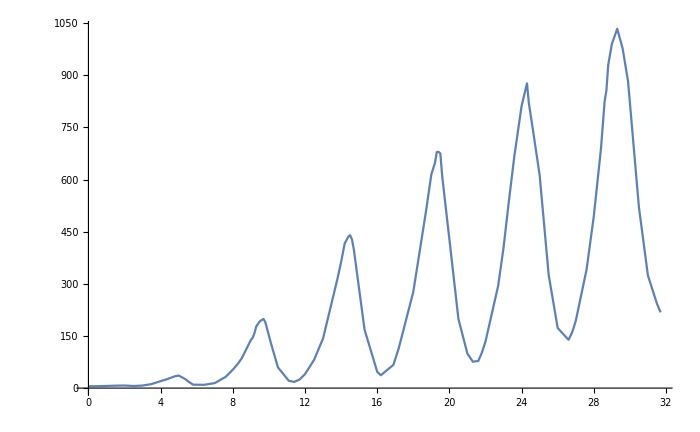

```mathematica
ListLinePlot[Table[{Hglist1[[i]],Hglist2[[i]]},{i,1,Length[Hglist1]}]]
```

```mathematica
Hglist3={22.0,22.7,23.1,23.4,23.7,24.0,24.3,24.4,24.6,24.8,25.2,25.6,26.1,26.3,26.5,27.0,27.3,27.5,28.0,28.3,28.7,29.0,29.3,29.6,30.1,30.7,31.1,31.7};
Hglist4={367,581,740,919,1098,1195,1183,1123,1007,850,601,424,355,365,399,536,617,705,942,1075,1306,1368,1335,1250,985,673,585,630};
Hglist5={22.0,22.6,23.0,23.6,23.8,23.9,24.0,24.1,24.3,24.4,24.5,24.7,25.0,25.5,26.0,26.4,26.6,26.7,26.9,27.0,27.6,28.1,28.5,28.8,29.2,29.3,29.5,29.7,29.8,30.0,30.7,31.0,31.2,31.7};
Hglist6={24.7,61.9,115.8,268.9,326.3,344.6,380.0,418.3,438.4,440,431,412,349,200,104,56.1,48.9,45.3,44.2,47.1,96.3,176.9,311.4,398.7,498,510,510,496,477,438,245,167,136,92};
```

```mathematica
Length[Hglist5]
```

34

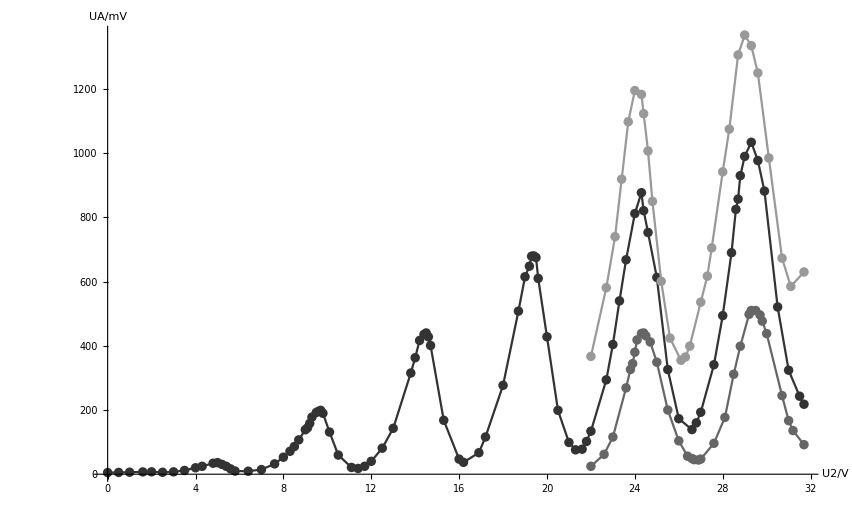

```mathematica
Show[ListLinePlot[Table[{Hglist1[[i]],Hglist2[[i]]},{i,1,Length[Hglist1]}],PlotStyle->{PointSize[0.008],Lighter[Black,0.2]}],ListPlot[Table[{Hglist1[[i]],Hglist2[[i]]},{i,1,Length[Hglist1]}],PlotStyle->{PointSize[0.008],Lighter[Black,0.2]}],ListLinePlot[Table[{Hglist3[[i]],Hglist4[[i]]},{i,1,Length[Hglist3]}],AxesOrigin->{0,0},PlotStyle->{PointSize[0.008],Lighter[Black,0.6]}],ListPlot[Table[{Hglist3[[i]],Hglist4[[i]]},{i,1,Length[Hglist3]}],AxesOrigin->{0,0},PlotStyle->{PointSize[0.008],Lighter[Black,0.6]}],ListLinePlot[Table[{Hglist5[[i]],Hglist6[[i]]},{i,1,Length[Hglist5]}],PlotStyle->{PointSize[0.008],Lighter[Black,0.4]}],ListPlot[Table[{Hglist5[[i]],Hglist6[[i]]},{i,1,Length[Hglist5]}],PlotStyle->{PointSize[0.008],Lighter[Black,0.4]}],PlotRange->All,AxesLabel->{"U2/V","UA/mV"}]
```

```mathematica
Grid[{{"Ukg2/V"}~Join~Hglist1[[1;;20]],{"Uout/mV"}~Join~Hglist2[[1;;20]],{"Ukg2/V"}~Join~Hglist1[[21;;40]],{"Uout/mV"}~Join~Hglist2[[21;;40]],{"Ukg2/V"}~Join~Hglist1[[41;;60]],{"Uout/mV"}~Join~Hglist2[[41;;60]],{"Ukg2/V"}~Join~Hglist1[[61;;80]],{"Uout/mV"}~Join~Hglist2[[61;;80]],{"Ukg2/V"}~Join~Hglist1[[81;;94]],{"Uout/mV"}~Join~Hglist2[[81;;94]]},Frame->All,Background->{None,{{White,Gray}}}]
```

Ukg2/V | 0. | 0.5 | 1. | 1.6 | 2. | 2.5 | 3. | 3.5 | 4. | 4.3 | 4.8 | 5. | 5.2 | 5.4 | 5.6 | 5.8 | 6.4 | 7. | 7.6 | 8.
Uout/mV | 5.2 | 5.5 | 6.2 | 7.1 | 7.4 | 6. | 7.3 | 11.7 | 20. | 24.6 | 34.2 | 36. | 30.7 | 24.6 | 16.5 | 9.9 | 9.4 | 14.4 | 32.2 | 53.
Ukg2/V | 8.3 | 8.5 | 8.7 | 9. | 9.1 | 9.2 | 9.3 | 9.5 | 9.6 | 9.7 | 9.8 | 10.1 | 10.5 | 11.1 | 11.4 | 11.7 | 12. | 12.5 | 13. | 13.8
Uout/mV | 71.4 | 86.3 | 107. | 138.5 | 144.6 | 158.3 | 177.8 | 192.4 | 195.8 | 198.9 | 189.8 | 131.3 | 59.6 | 21.1 | 17.9 | 24.7 | 40.2 | 81.1 | 143. | 315.2
Ukg2/V | 14. | 14.2 | 14.4 | 14.5 | 14.6 | 14.7 | 15.3 | 16. | 16.2 | 16.9 | 17.2 | 18. | 18.7 | 19. | 19.2 | 19.3 | 19.4 | 19.5 | 19.6 | 20.
Uout/mV | 362.8 | 416.6 | 435.5 | 440 | 428 | 401 | 168 | 47 | 37 | 67 | 116 | 277 | 508 | 615 | 648 | 679 | 680 | 675 | 610 | 428
Ukg2/V | 20.5 | 21. | 21.3 | 21.6 | 21.8 | 22. | 22.7 | 23. | 23.3 | 23.6 | 24. | 24.3 | 24.4 | 24.6 | 25. | 25.5 | 26. | 26.6 | 26.8 | 27.
Uout/mV | 199 | 99 | 76 | 78 | 102 | 134 | 294 | 404 | 540 | 668 | 812 | 877 | 821 | 753 | 613 | 326 | 173 | 139 | 160 | 193
Ukg2/V | 27.6 | 28. | 28.4 | 28.6 | 28.7 | 28.8 | 29. | 29.3 | 29.6 | 29.9 | 30.5 | 31. | 31.5 | 31.7 |  |  |  |  |  | 
Uout/mV | 341 | 494 | 690 | 825 | 857 | 930 | 990 | 1034 | 977 | 882 | 521 | 324 | 243 | 218 |  |  |  |  |  |

```mathematica
Grid[{{"Ukg2/V"}~Join~Hglist3[[1;;20]],{"Uout/mV"}~Join~Hglist4[[1;;20]],{"Ukg2/V"}~Join~Hglist3[[21;;28]],{"Uout/mV"}~Join~Hglist4[[21;;28]]},Frame->All,Background->{None,{{White,Gray}}}]
```

Ukg2/V | 22. | 22.7 | 23.1 | 23.4 | 23.7 | 24. | 24.3 | 24.4 | 24.6 | 24.8 | 25.2 | 25.6 | 26.1 | 26.3 | 26.5 | 27. | 27.3 | 27.5 | 28. | 28.3
Uout/mV | 367 | 581 | 740 | 919 | 1098 | 1195 | 1183 | 1123 | 1007 | 850 | 601 | 424 | 355 | 365 | 399 | 536 | 617 | 705 | 942 | 1075
Ukg2/V | 28.7 | 29. | 29.3 | 29.6 | 30.1 | 30.7 | 31.1 | 31.7 |  |  |  |  |  |  |  |  |  |  |  | 
Uout/mV | 1306 | 1368 | 1335 | 1250 | 985 | 673 | 585 | 630 |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
Grid[{{"Ukg2/V"}~Join~Hglist5[[1;;20]],{"Uout/mV"}~Join~Hglist6[[1;;20]],{"Ukg2/V"}~Join~Hglist5[[21;;34]],{"Uout/mV"}~Join~Hglist6[[21;;34]]},Frame->All,Background->{None,{{White,Gray}}}]
```

Ukg2/V | 22. | 22.6 | 23. | 23.6 | 23.8 | 23.9 | 24. | 24.1 | 24.3 | 24.4 | 24.5 | 24.7 | 25. | 25.5 | 26. | 26.4 | 26.6 | 26.7 | 26.9 | 27.
Uout/mV | 24.7 | 61.9 | 115.8 | 268.9 | 326.3 | 344.6 | 380. | 418.3 | 438.4 | 440 | 431 | 412 | 349 | 200 | 104 | 56.1 | 48.9 | 45.3 | 44.2 | 47.1
Ukg2/V | 27.6 | 28.1 | 28.5 | 28.8 | 29.2 | 29.3 | 29.5 | 29.7 | 29.8 | 30. | 30.7 | 31. | 31.2 | 31.7 |  |  |  |  |  | 
Uout/mV | 96.3 | 176.9 | 311.4 | 398.7 | 498 | 510 | 510 | 496 | 477 | 438 | 245 | 167 | 136 | 92 |  |  |  |  |  |

```mathematica
LinearModelFit[{17.0,28.2,39.8,52.1,64.4,77.6},x,x]
```

FittedModel[4.12667+12.1114 x]

```mathematica
%149["ParameterErrors"]
```

{0.656806,0.168652}

```mathematica
%149["AdjustedRSquared"]
```

0.999031

```mathematica
%149["ANOVATableMeanSquares"]
```

{2567.02,0.497762}

```mathematica
%149["BasisFunctions"]
```

{1,x}

```mathematica
%149["BestFit"]
```

4.12667+12.1114 x

```mathematica
%149["Response"]
```

{17.,28.2,39.8,52.1,64.4,77.6}

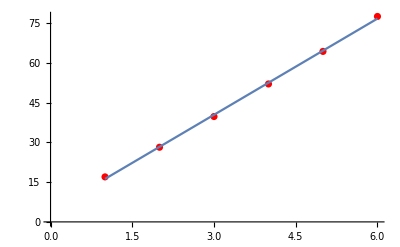

```mathematica
Show[ListPlot[{17.,28.2,39.8,52.1,64.4,77.6},PlotStyle->Red],Plot[%149[x],{x,1,6}]]
```

```mathematica
r=0.9990312178082428
```

0.999031

```mathematica
√(1/r^2-1)/(6-2)
```

```mathematica
0.008169850380254489*4.862857142857146
```

0.0397288

```mathematica
0.02202489297186395*12.111428571428565
```

0.266753

```mathematica
√(0.09+0.03)
```

0.34641

```mathematica
LinearModelFit[{5.0, 9.7, 14.5, 19.4 ,24.3, 29.3},x,x]
```

FittedModel[0.0133333+4.86286 x]

```mathematica
%161["BestFit"]
```

0.0133333+4.86286 x

```mathematica
%161["BasisFunctions"]
```

{1,x}

```mathematica
%161["AdjustedRSquared"]
```

```mathematica
r=0.9998665338141184
```

0.999867

```mathematica
√Sum[(n-3.5)^2,{n,1,6}]
```

4.1833

```mathematica
√(0.03972881527769471^2+(0.1/4.1833)^2)
```

0.046366

```mathematica
1/(4.1833*√3)
```

0.138013

```mathematica
√((2*1.6*10^-19*10)/(9.1*10^-31))
```

1.87523×10^6

```mathematica
distribution[u_,ua_,σ_]:=u^2*E^((-(u-ua)^2)/(2 σ^2))
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

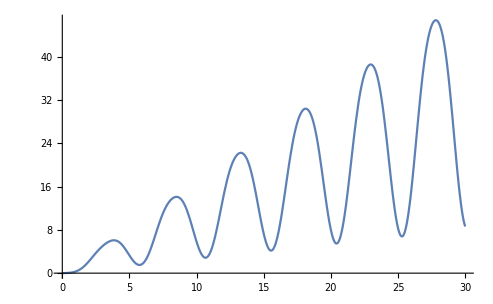

```mathematica
Plot[Sum[NIntegrate[distribution1[u,ua,0.7],{u,2+4.863x,4.863(x+1)}],{x,0,6}],{ua,0,30},PlotRange->All]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

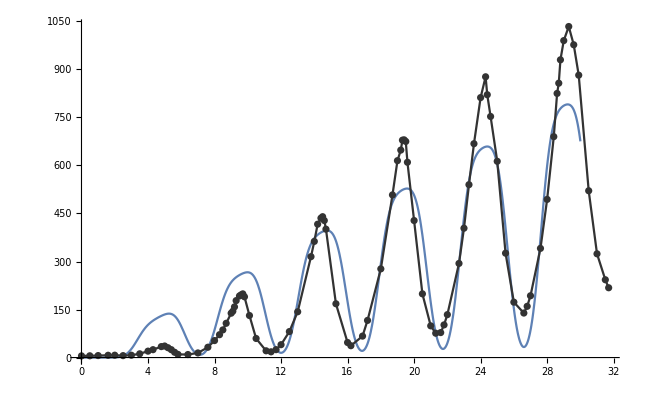

```mathematica
Show[Plot[Sum[NIntegrate[distribution1[u,ua,0.5],{u,1.3+2+4.863x,1.3+4.863(x+1)}],{x,0,6}]*1000/46,{ua,0,30},PlotRange->All],ListLinePlot[Table[{Hglist1[[i]],Hglist2[[i]]},{i,1,Length[Hglist1]}],PlotStyle->{PointSize[0.008],Lighter[Black,0.2]}],ListPlot[Table[{Hglist1[[i]],Hglist2[[i]]},{i,1,Length[Hglist1]}],PlotStyle->{PointSize[0.008],Lighter[Black,0.2]}]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

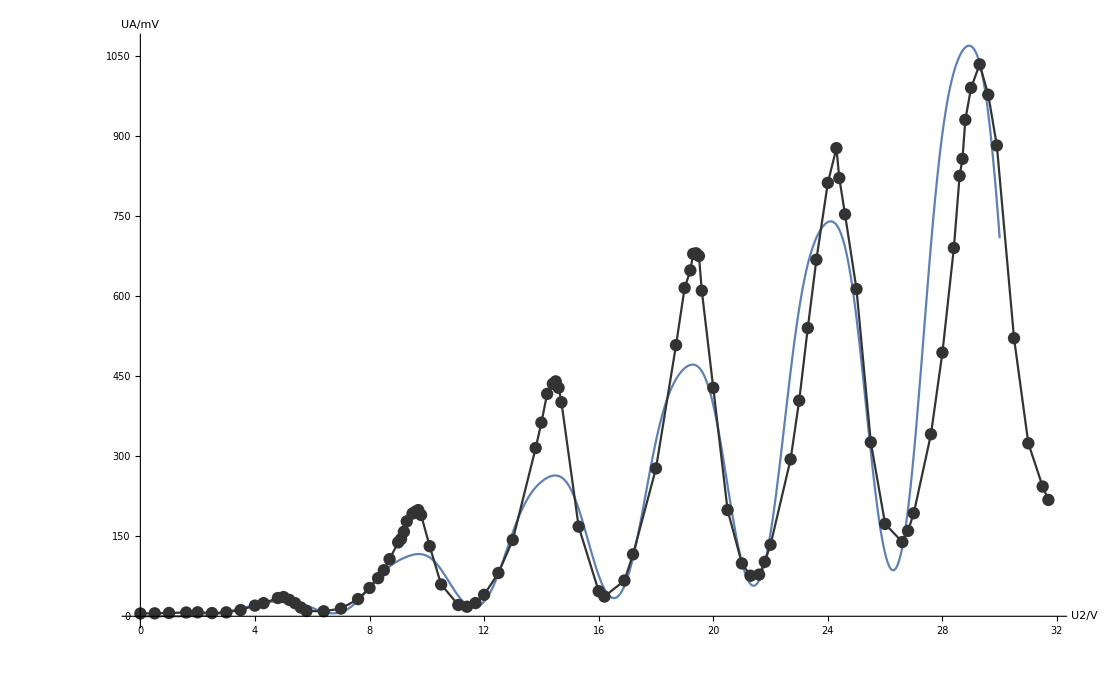

```mathematica
Show[Plot[Sum[NIntegrate[distribution[u,ua,0.6],{u,1+2+4.863x,1+4.863(x+1)}],{x,0,6}]/1.15,{ua,0,30},PlotRange->All],ListLinePlot[Table[{Hglist1[[i]],Hglist2[[i]]},{i,1,Length[Hglist1]}],PlotStyle->{PointSize[0.008],Lighter[Black,0.2]}],ListPlot[Table[{Hglist1[[i]],Hglist2[[i]]},{i,1,Length[Hglist1]}],PlotStyle->{PointSize[0.008],Lighter[Black,0.2]}],AxesLabel->{"U2/V","UA/mV"}]
```

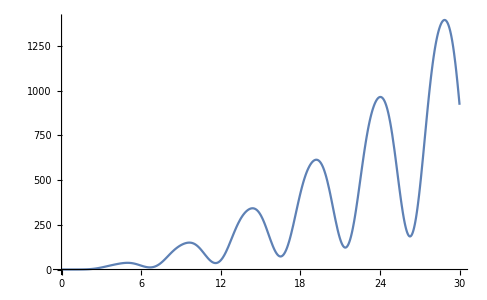
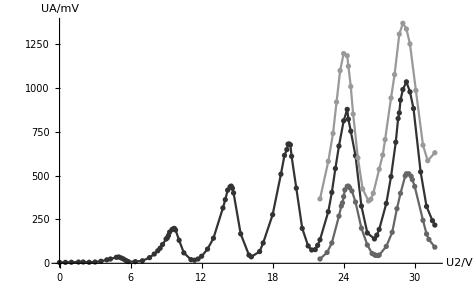

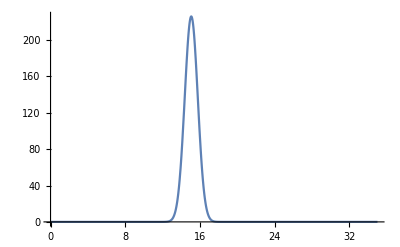

```mathematica
Plot[distribution[u,15,0.7],{u,0,35},PlotRange->All]
```

```mathematica
distribution1[u_,ua_,σ_]:=u*E^((-(u-ua)^2)/(2 σ^2))
```

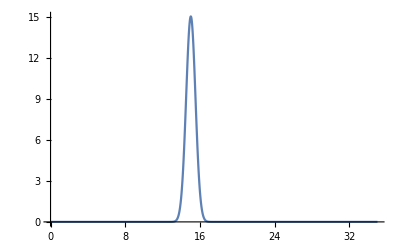

```mathematica
Plot[distribution1[u,15,0.5],{u,0,35},PlotRange->All]
```

```mathematica
∑_(x=0)^∞
```

```mathematica
∑_(x=0)^6 ∫_(4.863 x+2+1)^(4.863 (x+1)+1) distribution(u,ua,0.6)ⅆu
```